# ✨ Trapezium Rule ✨ Created by Haroon Sakhi

## 🌟 Introduction

The Trapezium Rule, also known as the trapezoidal rule, is a numerical method used to approximate the definite integral of a function. Unlike other methods, such as the midpoint or rectangular rule that use rectangles, the trapezium rule divides the area under the curve into trapezoidal segments. Summing the areas of these trapezoids generally provides a more accurate approximation, particularly when the function being integrated is smooth. This method is often employed when an exact analytical solution is either complex or unattainable.

## 🔢 Problem Setup

Consider a curve described by the function

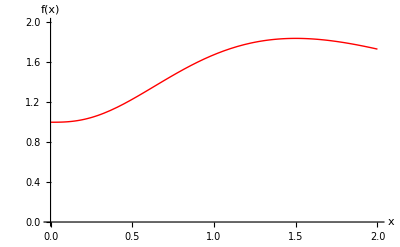

```mathematica
Plot[1+5x^3 Exp[-2x],{x,0,2},AxesOrigin->{0,0},PlotRange->{{0,2},{0,2}},GridLines->{{0},{0}},AxesLabel->{"x","f(x)"},PlotStyle->{Red,Thick}]
```

To compute the area under the curve, one would typically evaluate the definite integral:

However, exact integration is not always feasible. In such cases, numerical methods such as the trapezoidal rule are employed. This method approximates the area by dividing it into trapezoidal sections, which is conceptually similar to the Riemann sum but replaces rectangles with trapezoids.

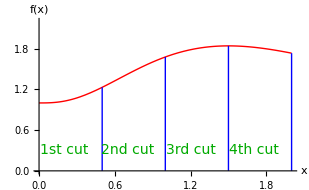

```mathematica
f[x_]:=1+5x^3 Exp[-2 x]
segmentPositions={0.5,1,1.5,2};
labelPositions={0.2,0.7,1.2,1.7}; 
labels={"1st cut","2nd cut","3rd cut","4th cut"};

Plot[f[x],{x,0,2},AxesOrigin->{0,0},PlotRange->{{0,2},{0,2.2}},AxesLabel->{"x","f(x)"},PlotStyle->{Red,Thick},Epilog->{Table[{Blue,Thick,Line[{{x,0},{x,f[x]}}]},{x,segmentPositions}],Table[Text[Style[labels[[i]],Darker[Green],14],{labelPositions[[i]],0.3}],{i,1,Length[labels]}]}]
```

## 📐 Generalized Expression

The area of a single trapezoid is given by:

where  and  are the lengths of the parallel sides, and  is the height.

where each trapezoid shares one parallel side with an adjacent trapezoid,the total area can be expressed as:

where  and  represent the lengths of the parallel sides at specific points.If the function is known these lengths can be expressed as function values at those points,resulting in:

By factoring out ,we obtain the following:

Generalizing this:

## 🛠️ Algorithm

Using above equation, the area under a curve for a specific domain can be computed by following these steps:

Define the domain,  and .

Discretize the domain into  intervals.

Compute the step size:

Sum the function values from  to .

Apply Equation to compute the total area.

## ✨ Example Problem

### 🔷 Defining the Function .

Consider the function:

```mathematica
F[x_]:=Exp[-2 x]
```

#### 📊 Visualization

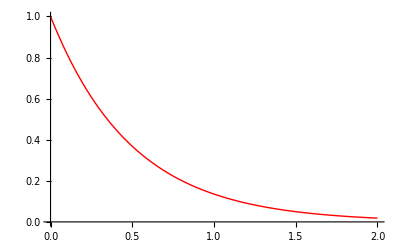

```mathematica
Plot[Exp[-2 x],{x,0,2},PlotStyle->{Thick,Red}]
```

### 🔷 Implement Trapezoidal Rule

```mathematica
TrapezoidalRule[start_,end_,numberOfCuts_]:=Module[{stepSize,K,x,Area},stepSize=(end-start)/numberOfCuts;
K=0;
x=start+stepSize;
Do[K+=F[x];
x+=stepSize,{i,1,numberOfCuts-1}];
Area=(stepSize/2) (F[start]+F[end])+stepSize K;N[Area]];
```

### 🔷 Parameters

```mathematica
xStart=0;   
xEnd=2;     
Ncuts=1000;
```

### 📊 Results

```mathematica
Print["Area: ",NumberForm[TrapezoidalRule[xStart,xEnd,Ncuts],{5,5}]];
```

Area: 0.49084

### 📊 Comparison of the number of intervals and percentage error

"Number of Intervals" | "Exact Area" | "Computed Area" | "% Error"
10 | 0.49084 | 0.4919 | 0.217
50 | 0.49084 | 0.49031 | 0.108
100 | 0.49084 | 0.49053 | 0.064
500 | 0.49084 | 0.49077 | 0.014
1000 | 0.49084 | 0.49081 | 0.007

## ⚠️ Conclusion

The accuracy of the trapezium rule is directly tied to the step size, $h$. A larger step size can result in significant errors. To achieve a higher degree of accuracy, the step size must be reduced, leading to a larger number of trapezoids. However, smaller step sizes increase the computational cost, as more function evaluations are required.
                Furthermore, the trapezium rule works best for smooth and continuous functions. If the function has discontinuities, sharp peaks, or highly oscillatory behavior, the trapezium rule may struggle to provide accurate results, even with a reduced step size. In such cases, other numerical integration methods may perform better.